```mathematica
mydata=Import[StringJoin[NotebookDirectory[],"data/ExampleFreezeOut.mx"]];
```

```mathematica
Export[StringJoin[NotebookDirectory[],"data/ExampleFreezeOut.csv"],Transpose@{
(Transpose@mydata["BackgroundFields"])[[1]],
(Transpose@mydata["BackgroundFields"])[[2]],
mydata["Alpha"],(*dimensionless*)
mydata["Time"],(*in fm/c*)
mydata["Radius"],(*in fm*)
mydata["TimeDerivative"],(*in fm/c*)
mydata["RadialDerivative"](*in fm*)
},"CSV"];
```

```mathematica
Export[StringJoin[NotebookDirectory[],"data/ExampleFreezeOut.txt"],{{1,2,3},{10,20,30}},"List"];
```

```mathematica
Keys[mydata]
```

{BackgroundFields,Alpha,Time,Radius,NumberOfPoints,TimeDerivative,RadialDerivative,MidpointRule,rStart,tStart,CentralityClass}

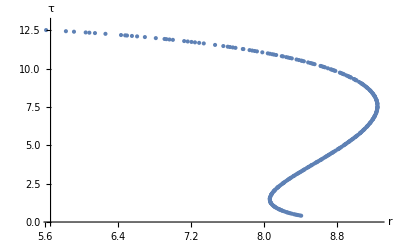

```mathematica
FreezeOutPlot=ListPlot[Transpose[{mydata["Radius"],mydata["Time"]}],AxesLabel->{r,τ}]
```

```mathematica
dalpha=mydata["Alpha"][[2;;]]-mydata["Alpha"][[1;;-2]];
ur=Sinh[ArcTanh[(Transpose@mydata["BackgroundFields"])[[1]][[1;;-2]]]]; (*dimensionless*)
utau=Cosh[ArcTanh[(Transpose@mydata["BackgroundFields"])[[1]][[1;;-2]]]]; (*dimensionless*)
```

```mathematica
Solve[a==(x+b)*(3*x-b)/(2*c),x]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{x→-0.01},{x→0.00333333}}

1

1.29812

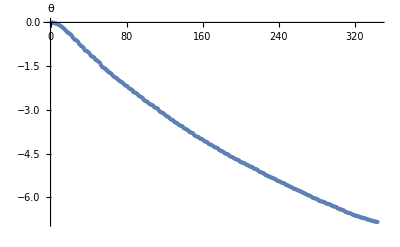

```mathematica
GeVtoIfm=1(*5.0677;(*1GeV=5.0677(fm^-1)\[hbar]c*)*)
IfmtoGeV=GeVtoIfm^(-1);
fmtoIGeV=GeVtoIfm;
IGeVtofm=fmtoIGeV^(-1);
mσ=0.6;(*mass of the sigma field ~ 400-800 MeV*)
ϵ=0.160054;(*energy density at freeze out GeV/(fm^3)*)
vev=1;(*vev of sigma field, in GeV*)
χ2=(-mσ^2+2*mσ*Sqrt[3*ϵ*(IfmtoGeV^3)/vev^2+mσ^2])/6;(*in GeV^2*)
χ=Sqrt[χ2];(*in GeV*)
θ0=0;

θ=θ0+χ*Accumulate[(mydata["TimeDerivative"][[1;;-2]]*utau-mydata["RadialDerivative"][[1;;-2]]*ur)*fmtoIGeV*dalpha];(*dimensionless*)
ρ=Sqrt[vev*(2*χ2+mσ^2)/(mσ^2)]
ϕfreeze=ρ*Exp[I*θ];
ThetaPlot=ListPlot[θ,AxesLabel->{None,"θ"}]
```

```mathematica
Integrate[Exp[I*(a*Cos[x])],{x,0,2*Pi},Assumptions->Element[a,Reals]]
```

6.28319+0. ⅈ

```mathematica
rs=mydata["Radius"][[1;;-2]];
drs=mydata["RadialDerivative"][[1;;-2]];
taus=mydata["Time"][[1;;-2]];
dtaus=mydata["TimeDerivative"][[1;;-2]];
```

```mathematica
mπ=0.14;(*in GeV, mπ0=134.9768 MeV, mπ+-=139.57039 MeV *)
ω[p_]=Sqrt[p^2+mπ^2];(*in GeV*)
J0rp[p_]=BesselJ[0,rs*p*GeVtoIfm];(*dimensionless*)
J1rp[p_]=BesselJ[1,rs*p*GeVtoIfm];(*dimensionless*)
Y0tw[p_]=BesselY[0,taus*ω[p]*GeVtoIfm];(*dimensionless*)
Y1tw[p_]=BesselY[1,taus*ω[p]*GeVtoIfm];(*dimensionless*)
J0tw[p_]=BesselJ[0,taus*ω[p]*GeVtoIfm];(*dimensionless*)
J1tw[p_]=BesselJ[1,taus*ω[p]*GeVtoIfm];(*dimensionless*)
helper0[p_]=I*ϕfreeze*χ*(-drs*utau+dtaus*ur)*J0rp[p]*(-Y0tw[p]+I*J0tw[p]);
helper1[p_]=dtaus*p*J1rp[p]*(-Y0tw[p]+I*J0tw[p]);
helper2[p_]=drs*J0rp[p]*ω[p]*(Y1tw[p]-I*J0tw[p]);
ϕfourier[p_]=-I*2*Pi^2*Total[dalpha*taus*rs*(helper0[p]-ϕfreeze*(helper1[p]+helper2[p]))];
```

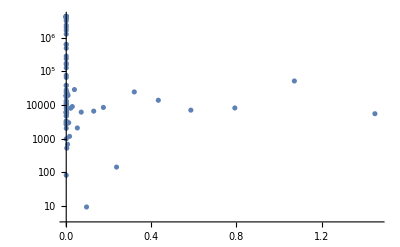

-Graphics-

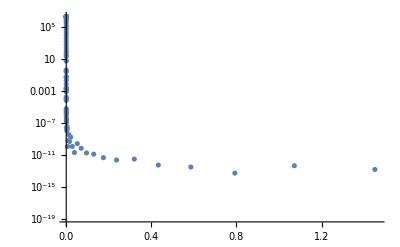

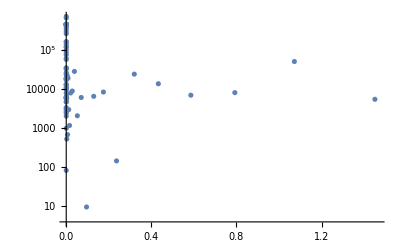

```mathematica
logspace[a_,b_,n_]:=10.0^Range[a,b,(b-a)/(n-1)];
ps=logspace[-3,10,100];(*in GeV*)
contrib1=2*Pi^2*Total[dalpha*taus*rs*(helper0[ps])];
contrib2=2*Pi^2*Total[dalpha*taus*rs*(ϕfreeze*(helper1[ps]+helper2[ps]))];
ListLogPlot[Transpose@{ps,Abs[ϕfourier[ps]]^2}]
ListLogPlot[Transpose@{ps,Abs[(contrib1-contrib2)^2]}]
ListLogPlot[Transpose@{ps,Abs[contrib1^2]}]
ListLogPlot[Transpose@{ps,Abs[contrib2^2]}]
```